# Ejercicio 3 - TP7

Pablo Chehade
8.06 - 0 pasos
8.18 - 2000 pasos
8.29 - 4000 pasos
9.00 - 9500 pasos

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Parámetros de la simulación*)
Nc = 30;
rho = 0.3;
L = (Nc^2/rho)^0.5;
Npasos = 20000;
h = 0.0005;
```

```mathematica
(*Quiero ver cómo se mueven las partículas*)
(*importo las posiciones*)
nombrex = "G:/Mi unidad/Pablo Chehade/Instituto Balseiro (IB)/Introducción a Física Computacional - FISCOM/Trabajos prácticos/TP 07/ejercicio1_tp07/mesh_position_x.dat";
nombrey = "G:/Mi unidad/Pablo Chehade/Instituto Balseiro (IB)/Introducción a Física Computacional - FISCOM/Trabajos prácticos/TP 07/ejercicio1_tp07/mesh_position_y.dat";

x = Import[nombrex, "FieldSeparators"->"\t"];
y = Import[nombrey, "FieldSeparators"->"\t"];
```

```mathematica
Manipulate[
ListPlot[Transpose[{x⟦t⟧,y⟦t⟧}], PlotRange->{{0,L},{0,L}}]
,{t,1,Npasos,1}]
```

```mathematica
(*Importo las energías*)
nombreEner = "G:/Mi unidad/Pablo Chehade/Instituto Balseiro (IB)/Introducción a Física Computacional - FISCOM/Trabajos prácticos/TP 07/ejercicio1_tp07/Energias.dat";
Energias =  Import[nombreEner, "FieldSeparators"->"\t"];
Ekin = Energias[[All,1]];
Epot = Energias[[All,2]];
Npasos = Length[Ekin];
```

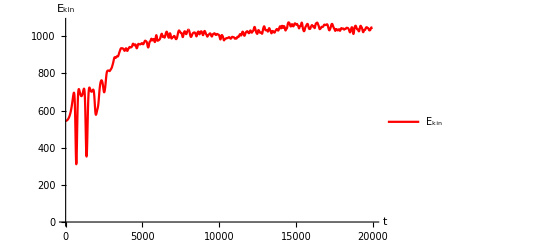

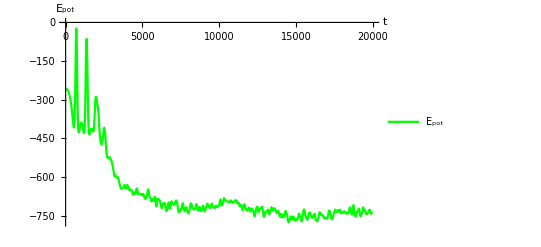

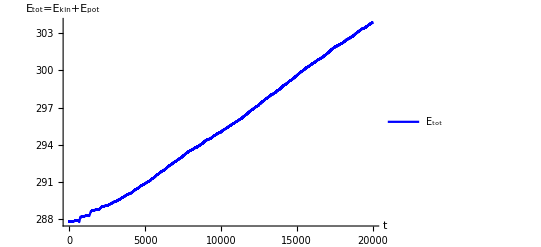

```mathematica
gkin = ListPlot[Transpose[{Range[Npasos], Ekin}], PlotStyle->Red, PlotRange->{All, All}, Joined->True,AxesLabel->{"t","E_kin"}, PlotLegends->{"E_kin"}] (*0,-Min[Epot]*)
gpot = ListPlot[Transpose[{Range[Npasos], Epot}], PlotStyle->Green,PlotRange->{All,All}, Joined->True,AxesLabel->{"t","E_pot"},PlotLegends->{"E_pot"}]
gsuma = ListPlot[Transpose[{Range[Npasos], Ekin + Epot}], PlotStyle->Blue, PlotRange->{All,All}, Joined->True, AxesLabel->{"t","E_tot=E_kin+E_pot"}, PlotLegends->{"E_tot"}]
(*Como la temperatura T es proporcional a la energía cinética por medio de kT = 3/2 E_cinetica, ya nos podemos dar una idea sobre cómo evoluciona la temperatura en el tiempo*)
```

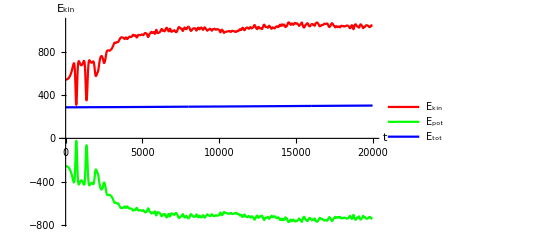

```mathematica
Show[{gkin,gpot,gsuma}, PlotRange->All]
(*error en la suma es por redondeo*)
```

```mathematica
(*Importo las velocidades*)
nombrevx = "G:/Mi unidad/Pablo Chehade/Instituto Balseiro (IB)/Introducción a Física Computacional - FISCOM/Trabajos prácticos/TP 07/ejercicio1_tp07/mesh_velocity_x.dat";
nombrevy = "G:/Mi unidad/Pablo Chehade/Instituto Balseiro (IB)/Introducción a Física Computacional - FISCOM/Trabajos prácticos/TP 07/ejercicio1_tp07/mesh_velocity_y.dat";
vx = Import[nombrevx, "FieldSeparators"->"\t"];
vy = Import[nombrevy, "FieldSeparators"->"\t"];
```

```mathematica
(*Defino |v|*)
v = (vx^2 + vy^2)^0.5;
```

```mathematica
(*Hago un histograma de vx y vy a tiempo t*)
bins = 0.01;
Manipulate[
Histogram[vx⟦t⟧,{bins}, PlotLabel->"P(v_x) a tiempo t = " <> ToString[t]]
,{t,1,Npasos,1}]
Manipulate[
Histogram[vy⟦t⟧,{bins}, PlotLabel->"P(v_y) a tiempo t = " <> ToString[t]]
,{t,1,Npasos,1}]
Manipulate[
Histogram[v⟦t⟧,{bins}, PlotLabel->"P(v) a tiempo t = " <> ToString[t]]
,{t,1,Npasos,1}]
```

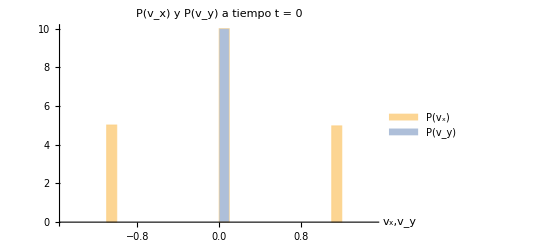

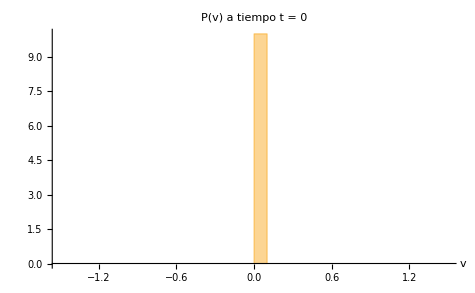

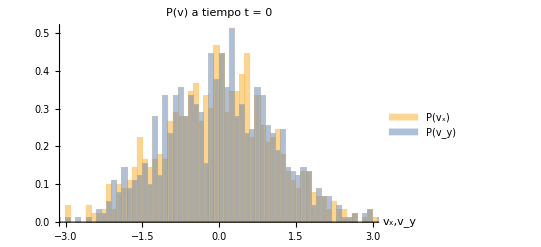

900

1800

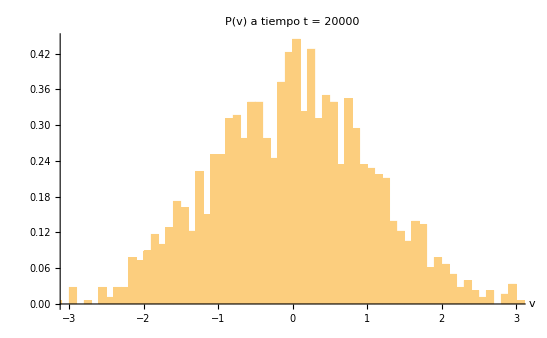

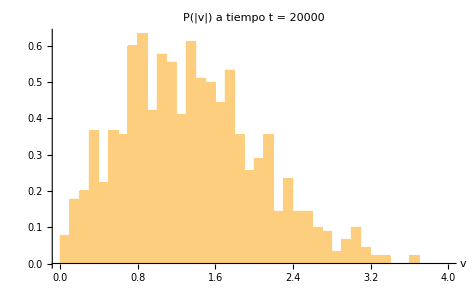

```mathematica
(*Grafico los histogramas anteriores para tiempo t=0, t= Npasos*)

bspec = 0.1;
vT = Append[vx⟦1⟧,vy⟦1⟧];
(*Histogram[vx⟦1⟧,{bspec},"PDF", PlotLabel->"P(v_x) a tiempo t = 0" ,AxesLabel->{"v_x"}, PlotRange->{{-1.5,1.5},All}]
Histogram[vy⟦1⟧,{bspec}, "PDF",PlotLabel->"P(v_y) a tiempo t = 0",AxesLabel->{"v_y"}, PlotRange->{{-1.5,1.5},All}]*)
Histogram[{vx⟦1⟧,vy⟦1⟧},{bspec}, "PDF",PlotLabel->"P(v_x) y P(v_y) a tiempo t = 0",AxesLabel->{"v_x,v_y"}, PlotRange->{{-1.5,1.5},All},ChartLegends->{"P(v_x)","P(v_y)"}]
Histogram[vT,{bspec}, "PDF",PlotLabel->"P(v) a tiempo t = 0",AxesLabel->{"v"}, PlotRange->{{-1.5,1.5},All}]

vT = Join[vx⟦Npasos⟧,vy⟦Npasos⟧];
bspec = 0.1;
(*Histogram[vx⟦Npasos⟧,{bspec}, "PDF",PlotLabel->"P(v_x) a tiempo t = " <> ToString[Npasos],AxesLabel->{"v_x"}, PlotRange->{{-3,3},All}]
Histogram[vy⟦Npasos⟧,{bspec}, "PDF",PlotLabel->"P(v_y) a tiempo t = " <> ToString[Npasos],AxesLabel->{"v_y"}, PlotRange->{{-3,3},All}]*)
Histogram[{vx⟦Npasos⟧,vy⟦Npasos⟧},{bspec}, "PDF",ChartLayout->"Overlapped",PlotLabel->"P(v) a tiempo t = 0",AxesLabel->{"v_x,v_y"}, PlotRange->{{-3,3},All},ChartLegends->{"P(v_x)","P(v_y)"}]
Length[vx⟦Npasos⟧]
Length[vT]
Histogram[vT,{bspec}, "PDF",PlotLabel->"P(v) a tiempo t = " <> ToString[Npasos],AxesLabel->{"v"}, PlotRange->{{-3,3},All}]
Histogram[v⟦Npasos⟧,{bspec}, "PDF",PlotLabel->"P(|v|) a tiempo t = " <> ToString[Npasos],AxesLabel->{"v"}, PlotRange->{{0,4},All}]
```

```mathematica
(*Guardo las alturas y las posiciones de la barras del histograma*)
bspec = 0.08;
{bins, alturas}=HistogramList[v⟦Npasos⟧,{bspec} , "PDF"];
bins = bins⟦1;;Length[bins]-1⟧; (*tengo más bins que alturas, centro todas las alturas en el bin de la izquierda*)
(*Ajusto con la distribución*)
data = Transpose[{bins,alturas}];

model[t_]:=d t E^{-e t^2 };
FindFit[data,model[t],{d,e},t]
```

{d→0.861025,e→0.43558}

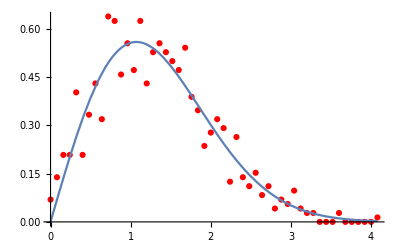

```mathematica
Show[ListPlot[data,PlotStyle->Red],Plot[model[t]/.{d->0.86102469814197,e->0.43558020308116385},{t,0.,4.08}]]
```

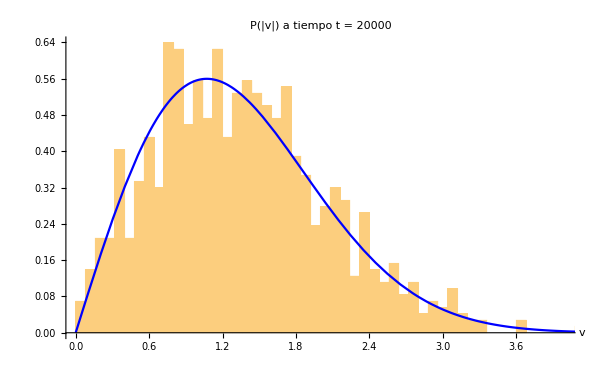

```mathematica
a = 0.86102469814197; (*= d*)
b = 0.43558020308116385; (*= c*)
fiteo[x_]:=a x E^{-b x^2 }
gdata = ListPlot[data,PlotStyle->Red];
ghist = Histogram[v⟦Npasos⟧,{bspec}, "PDF",PlotLabel->"P(|v|) a tiempo t = " <> ToString[Npasos],AxesLabel->{"v"}, PlotRange->{{0,4},All}];
gfit = Plot[fiteo[x],{x,0,5}, PlotStyle->Blue, PlotRange->All];
Show[{ghist,gfit}]
```

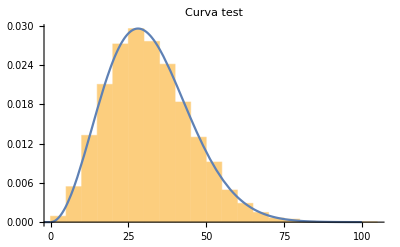

```mathematica
(*Grafico una distribución de Maxwell-Boltzmann*)
(*La distribución de MaxwellBolzmann en Mathematica es x^2 e^{-x^2/2sigma^2}.Entonces tomamos
1/2KT=1/2sigma^2,sigma^2=kT.*)
t = Npasos;
kT = 3/2 Ekin⟦t⟧;
sigma = √kT;

maxwell =ConstantArray[0,Npasos];
Do[
maxwell⟦j⟧=RandomVariate[MaxwellDistribution[sigma]]
,{j,1,Npasos}]

maxhist = Histogram[maxwell,Automatic,"PDF", PlotLabel->"Curva test"];
maxcurve = Plot[PDF[MaxwellDistribution[sigma],x],{x,-4,100}];
Show[{maxhist, maxcurve}]
(*Plot[Table[PDF[MaxwellDistribution[σ],x],{σ,{.5,.75,1.5}}]//Evaluate,{x,0,5},Filling->Axis,PlotRange->All]*)
```

```mathematica
(*Mathematica no tiene la distribución de Maxwell-Boltzmann en 2D, así que tengo que crearla yo*)
```